#### 10k steps, 50k samples, 1000 sites

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/kemal/Programs/MonteCarlo_for_JammedStates

```mathematica
data=ReadList["Data/classical_jammed.txt",Table[Real,4*250]];
```

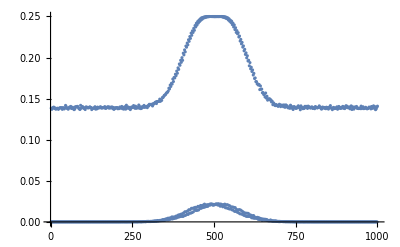

```mathematica
ListPlot[data[[6000]],PlotRange->All]
```

```mathematica
avg=data[[;;5000,;;]];
var=data[[5001;;10000,;;]];
```

```mathematica
Var=Table[Which[Mod[x,4]==1,(avg[[t,x]]-avg[[1,1]])^2,Mod[x,4]==2,(avg[[t,x]]-avg[[1,2]])^2,Mod[x,4]==3,(avg[[t,x]]-avg[[1,3]])^2,Mod[x,4]==0,(avg[[t,x]]-avg[[1,4]])^2],{t,5000},{x,1000}];
```

```mathematica
rays=Table[{(x-500.5)/(t+5000.),Var[[t,x]]},{t,5000},{x,1000}];
```

Let us take the top curve: in each quadruple of elements we choose the maximum. We assign this maximum to the average ray of the quadruple.

```mathematica
Rays=Table[{Mean[Transpose[#][[1]]],Max[Transpose[#][[2]]]}&/@Partition[rays[[t]],4],{t,5000}];
```

```mathematica
statistics=Module[{f,x,y},
Table[
f[x_]=Interpolation[Rays[[t]],x];
{2Abs[y]/.FindRoot[f[y]-0.5f[0.],{y,0.005}],f[0]},
{t,5000}]
];
```

```mathematica
stat=Table[{Log[N[t]],Log[statistics[[t-5000,1]]]},{t,5001,10000}];
```

```mathematica
g=LinearModelFit[stat,x,x];
```

```mathematica
k=D[g[x],x]
```

-0.527879

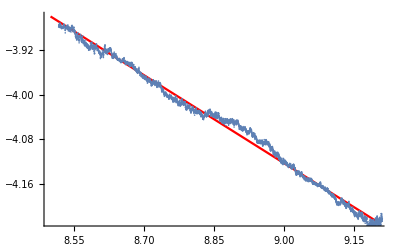

```mathematica
Show[Plot[g[x],{x,8.5,9.2},PlotStyle->Red],ListPlot[stat]]
```

```mathematica
stat2=Table[{t^k,statistics[[t-5000,1]]},{t,5001,10000}];
```

```mathematica
g2=LinearModelFit[stat2,x,x];
```

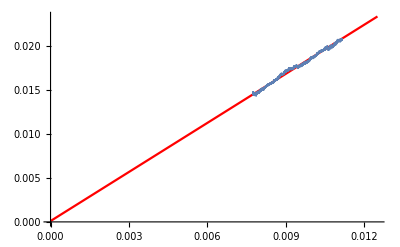

```mathematica
Show[Plot[g2[x],{x,0,0.0125},PlotStyle->Red],ListPlot[stat2]]
```

```mathematica
Manipulate[ListPlot[{{{statistics[[t,1]]/2,statistics[[t,2]]/2}},Rays[[t]]},PlotRange->{{-0.05,0.05},{-0.00001,0.5}},PlotStyle->{Blue,{Thin,Red}},Joined->{False,True}],{t,1,5000}]
```

Part::partd: Part specification statistics⟦1.,1⟧ is longer than depth of object.

Part::partd: Part specification statistics⟦1.,2⟧ is longer than depth of object.

Part::partd: Part specification Rays⟦1.⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ListPlot::lpn: {{{0.5 statistics⟦1.,1⟧,0.5 statistics⟦1.,2⟧}},{}} is not a list of numbers or pairs of numbers.

#### 20k steps, 50k samples, 1000 sites

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/lzadnik/Documents/Wolfram Mathematica

```mathematica
data=ReadList["classical_jammed_2.txt",Table[Real,4*250]];
```

```mathematica
avg=data[[;;15000,;;]];
var=data[[15001;;20000,;;]];
```

```mathematica
Var=Table[Which[Mod[x,4]==1,(avg[[t,x]]-avg[[1,1]])^2,Mod[x,4]==2,(avg[[t,x]]-avg[[1,2]])^2,Mod[x,4]==3,(avg[[t,x]]-avg[[1,3]])^2,Mod[x,4]==0,(avg[[t,x]]-avg[[1,4]])^2],{t,15000},{x,1000}];
```

```mathematica
rays=Table[{(x-500.5)/(t+5000.),Var[[t,x]]},{t,15000},{x,1000}];
```

Let us take the top curve: in each quadruple of elements we choose the maximum. We assign this maximum to the average ray of the quadruple.

```mathematica
Rays=Table[{Mean[Transpose[#][[1]]],Max[Transpose[#][[2]]]}&/@Partition[rays[[t]],4],{t,15000}];
```

```mathematica
statistics=Module[{f,x,y},
Table[
f[x_]=Interpolation[Rays[[t]],x];
{2Abs[y]/.FindRoot[f[y]-0.5f[0.],{y,0.005}],f[0]},
{t,15000}]
];
```

```mathematica
stat=Table[{Log[N[t]],Log[statistics[[t-5000,1]]]},{t,15001,20000}];
```

```mathematica
g=LinearModelFit[stat,x,x];
```

```mathematica
k=D[g[x],x]
```

-0.525851

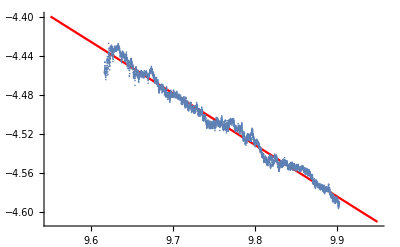

```mathematica
Show[Plot[g[x],{x,9.55,9.95},PlotStyle->Red],ListPlot[stat]]
```

```mathematica
stat2=Table[{t^k,statistics[[t-5000,1]]},{t,15001,20000}];
```

```mathematica
g2=LinearModelFit[stat2,x,x];
```

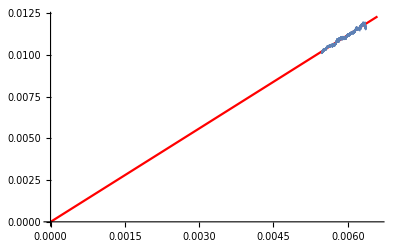

```mathematica
Show[Plot[g2[x],{x,0,0.0066},PlotStyle->Red],ListPlot[stat2]]
```

```mathematica
Manipulate[ListPlot[{{{statistics[[t,1]]/2,statistics[[t,2]]/2}},Rays[[t]]},PlotRange->{{-0.05,0.05},{-0.00001,0.5}},PlotStyle->{Blue,{Thin,Red}},Joined->{False,True}],{t,1,15000}]
```

Part::partd: Part specification statistics⟦1.,1⟧ is longer than depth of object.

Part::partd: Part specification statistics⟦1.,2⟧ is longer than depth of object.

Part::partd: Part specification Rays⟦1.⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ListPlot::lpn: {{{0.5 statistics⟦1.,1⟧,0.5 statistics⟦1.,2⟧}},{}} is not a list of numbers or pairs of numbers.

#### Solving the dynamics

```mathematica
σ:=PauliMatrix;
TP:=KroneckerProduct;
```

```mathematica
L=8;
h=TP[σ[1],σ[1]]+TP[σ[2],σ[2]];
q=TP[σ[1],σ[2]]-TP[σ[2],σ[1]];
P=SparseArray[{i_,j_}/;IntegerDigits[j-1,2,L]==RotateLeft[IntegerDigits[i-1,2,L]]->1,{2^L,2^L}];
```

```mathematica
Table[
x=RandomInteger[{0,1},L];
P.Table[If[IntegerDigits[j,2,L]==x,1,0],{j,0,2^L-1}]==Table[If[IntegerDigits[j,2,L]==RotateRight[x],1,0],{j,0,2^L-1}],
1000]//Union
```

{True}

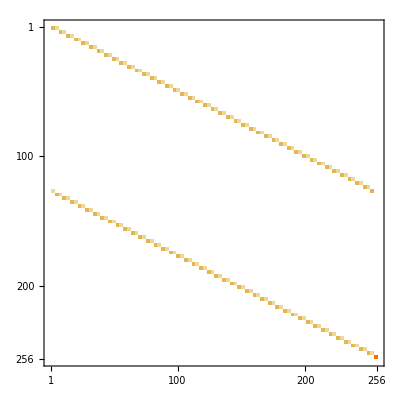

```mathematica
MatrixPlot[P]
```

```mathematica
Transpose[P].P-IdentityMatrix[2^L]//Flatten//Union
```

{0}

```mathematica
H[L_,k_]:=Module[{dum=h,dum2=σ[0]-σ[3],dum3=TP[σ[0]-σ[3],σ[0]]},
Do[dum=TP[σ[0],dum],L-2];
Do[dum2=TP[σ[0],dum2],L-1];
Do[dum3=TP[σ[0],dum3],L-2];
dum+Exp[-I k]dum2.P+Exp[I k]dum3.Transpose[P]];
Q[L_,k_]:=Module[{dum=q,dum2=-I(σ[0]-σ[3]),dum3=I TP[σ[0]-σ[3],σ[0]]},
Do[dum=TP[σ[0],dum],L-2];
Do[dum2=TP[σ[0],dum2],L-1];
Do[dum3=TP[σ[0],dum3],L-2];
dum+Exp[-I k]dum2.P+Exp[I k]dum3.Transpose[P]];
```

```mathematica
Q[L,0.2].H[L,0.2]-H[L,0.2].Q[L,0.2]//Chop//Flatten//Union
```

{0}

```mathematica
Table[eigs[L,k]=Sort[Eigenvalues[H[L,2.π k/L]]],{k,L}];
```

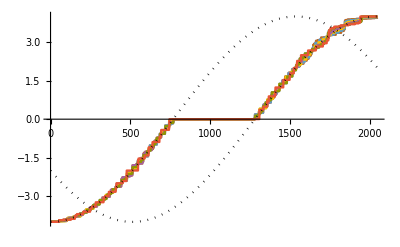

```mathematica
Show[ListPlot[Table[Chop[eigs[L,k]],{k,L}],Joined->True],ListPlot[Table[-4Cos[2/3 2π k/2^L],{k,2^L}],Joined->True,PlotStyle->{Black,Dotted}],
ListPlot[Table[-4Cos[2/3 2π (k-1/4 2^L)/2^L],{k,2^L}],Joined->True,PlotStyle->{Black,Dotted}]]
```

```mathematica
Table[pos[L,k]=eigs[L,k][[5/8 2^L;;]],{k,L}];
```

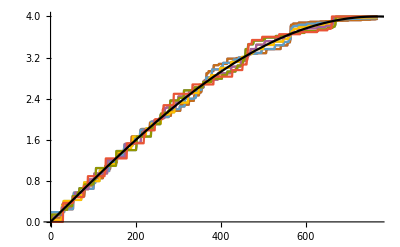

```mathematica
Show[ListPlot[Table[pos[L,k],{k,L}],Joined->True],ListPlot[Table[4Sin[2/3 2π k/2^L],{k,2^L}],Joined->True,PlotStyle->Black]]
```

```mathematica
var[L]=Mean[Variance/@Transpose[Table[eigs[L,k],{k,L}]]];
```

```mathematica
fit=N[Table[{Log[l],Log[var[l]]},{l,8,12}]];
```

```mathematica
f[y_]=LinearModelFit[fit,y,y]//Normal;
```

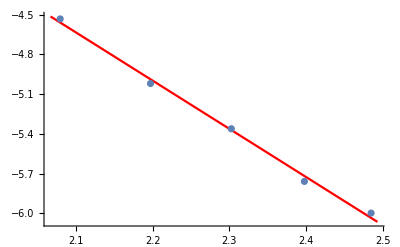

```mathematica
Show[Plot[f[y],{y,Log[7.9],Log[12.1]},PlotStyle->Red],ListPlot[fit]]
```

```mathematica
D[f[y],y]
```

-3.64157

```mathematica
D[ArcCos[-X/4/J],X]//FullSimplify
```

1/(J √(16-X^2/J^2))

#### Relevant sectors

```mathematica
L=14;
```

```mathematica
cy:=DeleteDuplicates[Permute[#,CyclicGroup[Length@#]]]&
```

```mathematica
η=0;
configs={};
Module[{nn(*number of particles*),m(*its digits give configuration*)},
For[nn=1,nn≤L,++nn,
exclusion={}(*integers that give the same configuration up to cyclic shifts*);
For[m=0,m<=2^nn-1,++m,
If[MemberQ[exclusion,m],Continue[]];
num=IntegerDigits[m,2,nn];
MM=Sum[num[[j]](1-num[[j+1]]) ,{j,1,nn-1}]+num[[nn]](1-num[[1]])(*number of switches - -> +*);
If[nn>L/2+MM,Continue[]](*for each switch - -> +, you can get another particle*);
exclusion=Join[exclusion,FromDigits[#,2]&/@cy[num][[2;;-1]],1](*we add all cyclic shifts of the current configuration to exclusions*);
AppendTo[configs,IntegerDigits[m,2,nn]];
]
]]
Energies={};
For[p=1,p≤Length[configs],++p,
momenta={};
s=configs[[p]];
n=Length[s];
sALL=cy[s];
nred=Length[sALL](*length of the sub-symmetry cell*);
M=Sum[s[[j]](1-s[[j+1]]) ,{j,1,n-1}]+s[[n]](1-s[[1]])(*number of switches - -> +*);
QNum=Subsets[Range[0, L/2+M-1],{n}](*possible sets of quantum numbers*);
For[J0=0,J0< nred,++J0,
For[z=1,z≤Length[QNum],++z,
J=QNum[[z]];
P=Table[2Pi/(L/2+M)(J[[l]]+2M/L/n Total[J])+2Pi (η+n/nred-1)/L+4Pi J0/L/nred,{l,n}];
If[!MemberQ[momenta,Sort[Mod[P,2Pi]]],
AppendTo[Energies,{nred,n,M,J0,J,s,Sort[Mod[P,2Pi]]}];
AppendTo[momenta,Sort[Mod[P,2Pi]]];
];
];
];
];
```

```mathematica
reducedConfs=Cases[Energies,_?(L/2+#[[3]]==#[[2]]+1∨L/2+#[[3]]==#[[2]]&)];
Length[reducedConfs]
```

4105

```mathematica
sortedE[L]=Sort[Total[4Cos[N[#]]]&/@reducedConfs[[;;,-1]]//Chop];
```

```mathematica
DeleteDuplicates[sortedE[L],(Abs[#1-#2]<0.0001&)]
```

{-4.,-3.99667,-3.99503,-3.99178,-3.9839,-3.97485,-3.97007,-3.95532,-3.93572,-3.92624,-3.91706,-3.89971,-3.87631,-3.85585,-3.83797,-3.79622,-3.77553,-3.75877,-3.74494,-3.73335,-3.60388,-3.45042,-3.4338,-3.41316,-3.3869,-3.35235,-3.27401,-3.23607,-3.18853,-3.12733,-3.0758,-3.04578,-3.01229,-2.93221,-2.85713,-2.82843,-2.76425,-2.6892,-2.64674,-2.61944,-2.49396,-2.36432,-2.33497,-2.28847,-2.20359,-2.12813,-2.09347,-2.,-1.89547,-1.85015,-1.80869,-1.73553,-1.64515,-1.5721,-1.51187,-1.38146,-1.32112,-1.27395,-1.23607,-1.20498,-0.890084,-0.569259,-0.536933,-0.497375,-0.447858,-0.384092,-0.244647,-0.179459,-0.0997228,0,0.0815941,0.128206,0.179459,0.29892,0.407292,0.447858,0.536933,0.6384,0.694593,0.730279,0.890084,1.04841,1.08336,1.13811,1.23607,1.32112,1.35956,1.46136,1.5721,1.61913,1.66166,1.73553,1.82484,1.89547,1.9527,2.07357,2.12813,2.17019,2.20359,2.23075,2.49396,2.74057,2.76425,2.79295,2.82843,2.8734,2.96894,3.01229,3.06418,3.12733,3.17755,3.20565,3.23607,3.30496,3.36501,3.3869,3.4338,3.48527,3.51289,3.53009,3.60388,3.67167,3.6859,3.70767,3.74494,3.77553,3.78881,3.82229,3.85585,3.86918,3.88074,3.89971,3.92069,3.93572,3.94685,3.96716,3.97485,3.98012,3.9839,3.98669,4.}

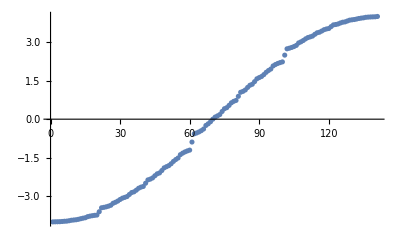

```mathematica
ListPlot[%]
```

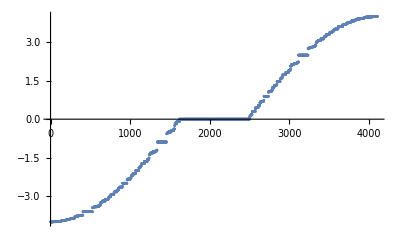

```mathematica
ListPlot[sortedE[L]]
```

```mathematica
jammed[L]=Length[Cases[reducedConfs,_?(Abs@Total[4.Cos[#[[-1]]]]<0.00001&&L/2+#[[3]]=!=#[[2]]&)]];
zero[L]=Length[Cases[reducedConfs,_?(Abs@Total[4.Cos[#[[-1]]]]<0.00001&)]];
all[L]=Length[reducedConfs];
```

```mathematica
sortedStates=SortBy[Flatten[#,1]&/@({#[[1;;6]],Total[4Cos[N[#[[-1]]]]]}&/@reducedConfs//Chop),#[[-1]]&];
sortedStates[[;;,-1]]-sortedE[L]//Chop//Union
```

{0}

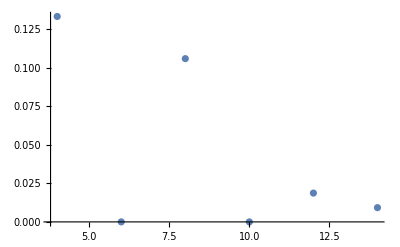

```mathematica
ListPlot[Table[{l,jammed[l]/all[l]},{l,4,14,2}]]
```

```mathematica
confData=reducedConfs[[;;,{2,3,4,5,7}]];
confData=({#[[1]],#[[2]],#[[3]],First[Complement[Range[0,#[[1]]],#[[4]]]],#[[5]]}&/@confData);
```